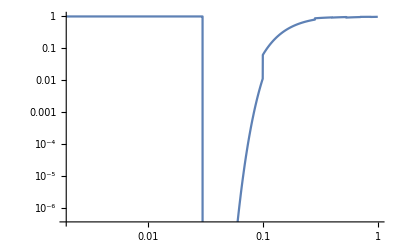

```mathematica
Clear["Global`*"]
y[x_]:=Piecewise[{
{1.688*10^(-22)*x^(1.77),1100<x<4800},
{1,0.25<x<5}}];


c0[x_]:=Piecewise[{
{17.3,0.030<x<0.100},
	{34.6,0.100<x<0.284},
	{78.1,0.284<x<0.400},
{71.4,0.400<x<0.532},
	{95.5,0.532<x<0.707},
	{308.9,0.707<x<0.867},
	{120.6,0.867<x<1.303},
	{141.3,1.303<x<1.840},
	{202.7,1.840<x<2.471},
	{342.7,2.471<x<3.210},
	{352.2,3.210<x<4.038},
	{433.9,4.038<x<7.111},
	{629.0,7.111<x<8.331},
	{701.2,8.331<x<10.000}},0];

c1[x_]:=Piecewise[{
{608.1,0.030<x<0.100},
	{267.9,0.100<x<0.284},
	{18.8,0.284<x<0.400},
{66.8,0.400<x<0.532},
	{145.8,0.532<x<0.707},
	{-380.6,0.707<x<0.867},
	{169.3,0.867<x<1.303},
	{146.8,1.303<x<1.840},
	{104.7,1.840<x<2.471},
	{18.7,2.471<x<3.210},
	{18.7,3.210<x<4.038},
	{-2.4,4.038<x<7.111},
	{30.9,7.111<x<8.331},
	{25.2,8.331<x<10.000}},0];

c2[x_]:=Piecewise[{
{-2150.,0.030<x<0.100},
	{-476.1,0.100<x<0.284},
	{4.3,0.284<x<0.400},
{-51.4,0.400<x<0.532},
	{-61.1,0.532<x<0.707},
	{294.0,0.707<x<0.867},
	{-47.7,0.867<x<1.303},
	{-31.5,1.303<x<1.840},
	{-17.0,1.840<x<2.471},
	{0.0,2.471<x<3.210},
	{0.0,3.210<x<4.038},
	{0.75,4.038<x<7.111},
	{0.0,7.111<x<8.331},
	{0.0,8.331<x<10.000}},0];

sigma[energy_]:=(c0 [energy]energy+c1[energy] energy+c2[energy] energy^2)energy^(-3)*10^(-24);
Nh:=10.9*10^(19);
extinctionCurve[x_]:=Exp[-sigma[x]*Nh];
LogLogPlot[Exp[-sigma[x]*Nh],{x,0.,1}]
```

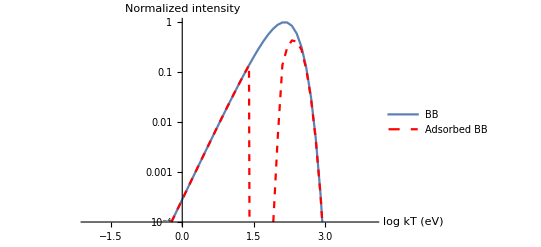

```mathematica
Clear["Global`*"]

(*Температура*)
T:=50;


(*Спектр ЧТ*)
Planck[w_]:=w^3/(4 Pi^3)/(Exp[w/T]-1);

(*Импорт данных*)
energyLogValues=Range[-2,4,0.1];
energyValues = 10^x/.x->energyLogValues;

(*Расчет спектра ЧТ*)
planckValues := Planck[energyValues]/Max[ Planck[energyValues]];

(*Коэффициенты кривой поглощения*)
c0[x_]:=Piecewise[{
{17.3,0.030<x<=0.100},
	{34.6,0.100<=x<0.284},
	{78.1,0.284<=x<0.400},
{71.4,0.400<=x<0.532},
	{95.5,0.532<=x<0.707},
	{308.9,0.707<=x<0.867},
	{120.6,0.867<=x<1.303},
	{141.3,1.303<=x<1.840},
	{202.7,1.840<=x<2.471},
	{342.7,2.471<=x<3.210},
	{352.2,3.210<=x<4.038},
	{433.9,4.038<=x<7.111},
	{629.0,7.111<=x<8.331},
	{701.2,8.331<=x<10.000}},0];
c1[x_]:=Piecewise[{
{608.1,0.030<x<=0.100},
	{267.9,0.100<=x<0.284},
	{18.8,0.284<=x<0.400},
{66.8,0.400<=x<0.532},
	{145.8,0.532<=x<0.707},
	{-380.6,0.707<=x<0.867},
	{169.3,0.867<=x<1.303},
	{146.8,1.303<=x<1.840},
	{104.7,1.840<=x<2.471},
	{18.7,2.471<=x<3.210},
	{18.7,3.210<=x<4.038},
	{-2.4,4.038<=x<7.111},
	{30.9,7.111<=x<8.331},
	{25.2,8.331<=x<10.000}},0];
c2[x_]:=Piecewise[{
{-2150.,0.030<x<=0.100},
	{-476.1,0.100<=x<0.284},
	{4.3,0.284<=x<0.400},
{-51.4,0.400<=x<0.532},
	{-61.1,0.532<=x<0.707},
	{294.0,0.707<=x<0.867},
	{-47.7,0.867<=x<1.303},
	{-31.5,1.303<=x<1.840},
	{-17.0,1.840<=x<2.471},
	{0.0,2.471<=x<3.210},
	{0.0,3.210<=x<4.038},
	{0.75,4.038<=x<7.111},
	{0.0,7.111<=x<8.331},
	{0.0,8.331<=x<10.000}},0];

(*Сигма, кол-во атомов водорода *)
sigma[energy_]:=(c0 [energy]energy+c1[energy] energy+c2[energy] energy^2)energy^(-3)*10^(-24);
Nh:=12.9*10^(19);

(*Кривая поглощения, переводим энергию в keV*)
extinctionCurve[energyEv_]:=Exp[-sigma[energyEv*0.001]*Nh];

(*Modification factor для поглощения*)
adsorbtionValues:=extinctionCurve/@energyValues;

(*Расчет спектра с поглощением*)
adsorbedPlanckValues=Planck[energyValues]*adsorbtionValues/Max[Planck[energyValues]];

(*Вывод графиков, energyValues для обычной, energyLogValues для логарифмической*)
plotUnmixed = ListLogPlot[Transpose[{energyLogValues, planckValues}],
PlotRange->{{-2,4},{0.0001,1}},PlotLegends->{"BB" },Joined->True];

plotMixed =  ListLogPlot[Transpose[{energyLogValues, adsorbedPlanckValues}],PlotStyle->{Red,Dashed},
PlotRange->{{-2,4},{0.0001,1}},PlotLegends->{"Adsorbed BB" },Joined->True];

Show[plotUnmixed,plotMixed, AxesLabel->{"log kT (eV)","Normalized intensity"} ]
```

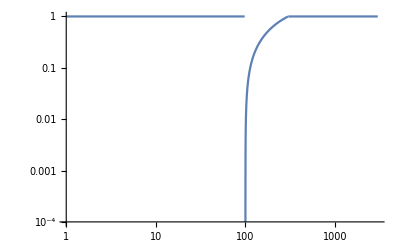

```mathematica
extinctionCurve[x_]:=Piecewise[{
{1-x^(-3)/(13.6)^(-3),13.6<x<300}},
	1];
(*0.034*)
expFactor = -1;
expCurve[x_]:=Piecewise[{
{(1-Exp[-(x-100)/200])/(1-Exp[-1]),98<x<300}},
	1];
LogLogPlot[{expCurve[x]},{x,1,3000}, PlotRange->{{All,All},{0.0001,1}}]
```

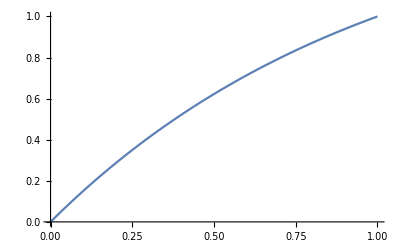

```mathematica
Plot[(1-Exp[-x])/(1-Exp[-1]),{x,0,1},]
```

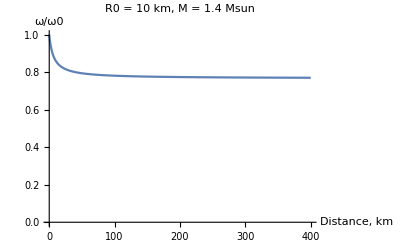

```mathematica
Clear["Global`*"]
redshift[x_]:=Sqrt[(1-(4.134/10))/(1-(4.134/(x+10)))];
Plot[redshift[x],{x,0,400},PlotRange->{{All,All},{0,1}},AxesLabel->{"Distance, km","ω/ω0"}, PlotLabel->"R0 = 10 km, M = 1.4 Msun"]
```